2019-03-28

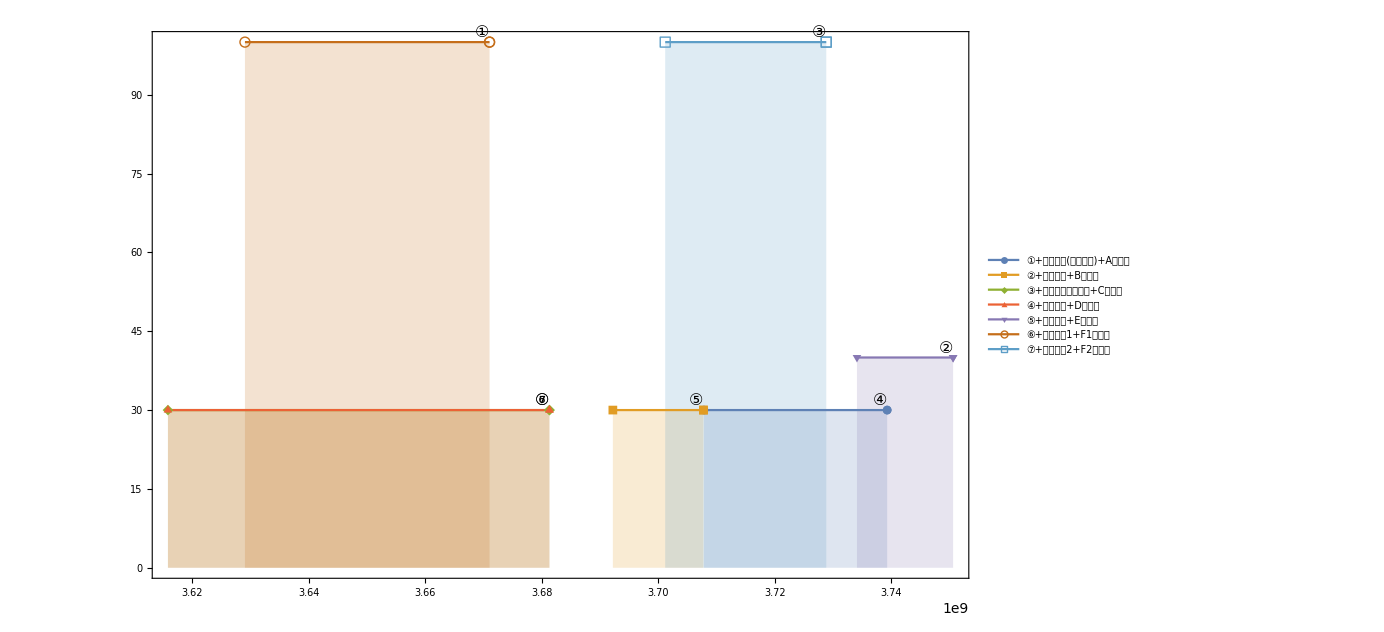

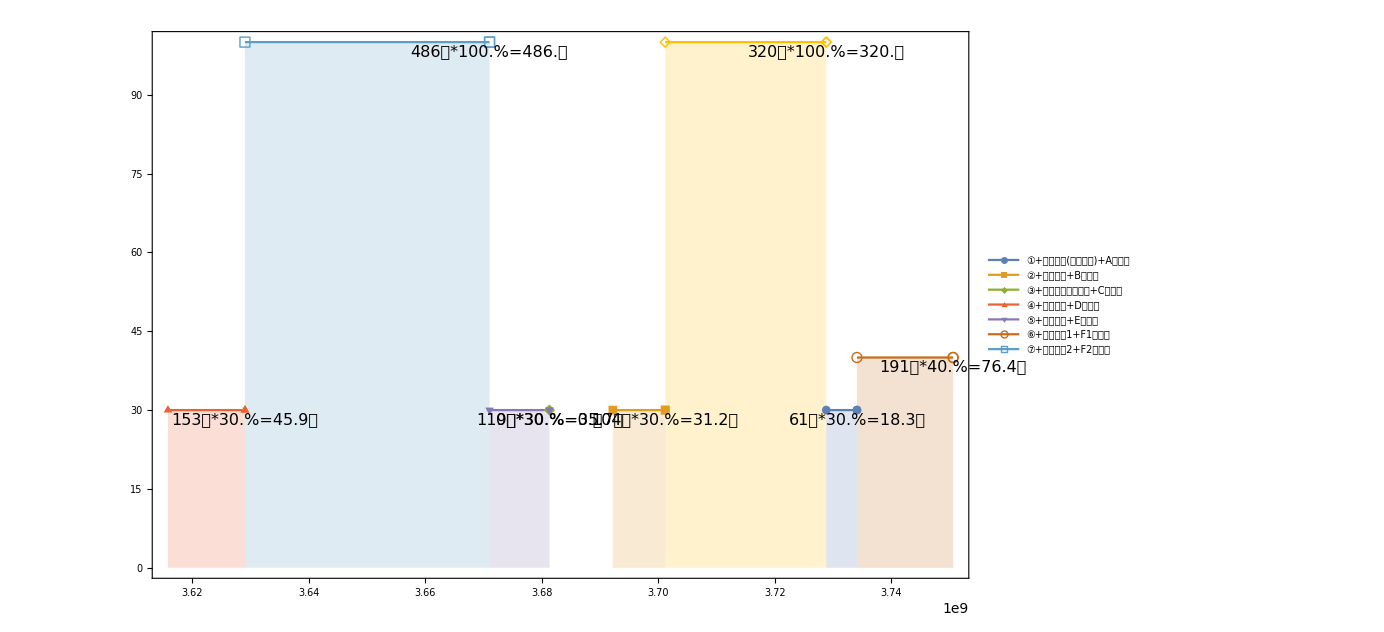

일련번호 | 근무처 | 직위(직급) | 시작일 | 종료일 | 기간(일) | 중복 내용 | 중복제외경력(H,일) | 인정율(I,%) | 유효경력(J=H*I,일) | 유효경력(=H*I,년월일) | 총 유효경력(=Σ J, 일수) | 총 유효경력(=Σ J,년월일)
① | A대학교 | 특강강사(영어강의) | 2015-01-01 | 2016-05-01 | 486 |  | 486 | 100. | 486. | 01년04월01일 |  | 
② | B대학교 | 시간강사 | 2018-05-01 | 2018-11-08 | 191 |  | 191 | 40. | 76.4 | 00년02월16일 |  | 
③ | C대학교 | 박사후과정연구원 | 2017-04-15 | 2018-03-01 | 320 |  | 320 | 100. | 320. | 00년10월20일 |  | 
④ | D대학교 | 시간강사 | 2017-07-01 | 2018-06-30 | 364 | {②, ③}번 경력에 중복됨 | 61 | 30. | 18.3 | 00년00월18일 | 1013.5 | 02년09월13일
⑤ | E대학교 | 시간강사 | 2017-01-01 | 2017-06-30 | 180 | {③}번 경력에 중복됨 | 104 | 30. | 31.2 | 00년01월01일 |  | 
⑥ | F1대학교 | 시간강사1 | 2014-08-01 | 2016-08-28 | 758 | {①, ⑦}번 경력에 중복됨 | 0 | 30. | 0. | 00년00월00일 |  | 
⑦ | F2대학교 | 시간강사2 | 2014-08-01 | 2016-08-28 | 758 | {①}번 경력에 중복됨 | 272 | 30. | 81.6 | 00년02월21일 |  |

```mathematica
(* step 1.1 그래프 그리기 ============================================================================*)
bPrintMsg = False; (*디버깅용 데이터 출력 여부*)
Block[{$DateStringFormat={"Year","-","Month","-","Day"}},DateString[]]
filename0 = SystemDialogInput["FileOpen",".xls"];
dir0 = DirectoryName[filename0];
excel0=Import[filename0] [[1]];
If[bPrintMsg,Print["엑셀 원본 =",excel0]];
excel1 = SortBy[ excel0, Last]//TableForm;
If[bPrintMsg,Print["가중치 기준 정렬 후 엑셀 =",excel1]];
length0               = Length[excel1[[1]]];(*경력의 총 개수=엑셀 row count*)

(*소팅 전 엑셀 데이터의 ID, 소속기관, 직급 (그래프 legend용) *)
excel0 = TableForm[excel0];
id0                        = excel0[[1]][[All,1]];
affilliation0 = excel0[[1]][[All,2]];(*엑셀의 두번째 column: 소속기관(display용.없어도 됨 ) *)
title0                 = excel0[[1]][[All,3]];(*엑셀의 세번째 column: 직급(display용.없어도 됨 ) *)

(*소팅 후 엑셀 데이터의 ID, 소속기관, 직급 등 (메인 작업용) *)
id1                        = excel1[[1]][[All,1]];
affilliation1 = excel1[[1]][[All,2]];
title1                 = excel1[[1]][[All,3]];
startdate1        =DateObject[excel1[[1]][[All,4]][[All,1]]  ,DateFormat-> {"Year", "-","Month","-","Day"}] ;(*엑셀의 네번째 column: 경력 시작일자(2013-01-01와 같은 엑셀 date 포맷) *)
enddate1             =DateObject[ excel1[[1]][[All,5]][[All,1]],
 DateFormat-> {"Year", "-","Month","-","Day"}] ;(*엑셀의 다섯 번째 column: 경력 종료일자(2013-01-01와 같은 엑셀 date 포맷) *)
weight1               =excel1[[1]][[All,6]];(*엑셀의 여섯 번째 column: 가중치(숫자. 0~100 범위) *)

wdateList1= Table[{{startdate1[[i]],weight1[[i]]},{enddate1[[i]],weight1[[i]]}},{i,1,length0}];(*weight date list*)
wdateVectors1 = Table[ {wdateList1[[i]]},{i, 1, length0}];(*weight date 의 벡터 list*)

graph1=DateListPlot[wdateList1,PlotRange->All,Filling->Axis,PlotLabels->Placed[id1,Above],PlotLegends->Placed[id0+title0+affilliation0,Bottom],ImageSize->{1024,768},LabelStyle->Directive[Black,FontFamily->"굴림",FontSize->16],PlotMarkers->Automatic]
(*마커에 Label표시하는 기능은 Mathematica 11.0부터 지원한단다. 
https://www.wolfram.com/language/11/visualization--labels-scales-exclusions/auto-labeling-data.html?product=mathematica *)
Export[dir0<>FileBaseName[filename0]<>".Graph1(RawData).bmp",graph1]; (*원본 파일과 같은 경로에 .bmp로 저장 *)


(*  step 1.2 실제 경력 날짜 계산 =============================================================================*)
ATimeItv0 =  Table[ Interval[ {0,0}], {i, 1, length0}];(*계산용으로 년월일을 절대시간으로 변환*)
EffectiveDays0 =  Table[ 0, {i, 1, length0}]; (*중복을 제외하고, 가중치를 곱하지 않은 경력일수 *)
EffectiveDays1 =  Table[ 0, {i, 1, length0}]; (*중복을 제외하고, 가중치를 곱한 실제 경력일수 *)
EffectiveDaysString1 = Table[ "", {i, 1, length0}];(*경력 년/월/일 포맷 문자열*)
TotalEffectiveDays0 = Table[ "",{i, 1, length0}];(* 번호별 가중치곱하지 않은 경력일수의 총합*)
TotalEffectiveDays1 = Table[ "",{i, 1, length0}];(* 번호별 실제 경력일수의 총합*)
TotalEffectiveDaysString1 = Table[ "",{i, 1, length0}];(* 번호별 실제 경력일수의 총합의 년/월/일 포맷 문자열*)
CoveringDates1 = Table[{},{i, 1, length0}];(*충돌하는 경력 번호*)
 CoveringDatesString1 = Table["",{i, 1, length0}];(*충돌하는 경력 번호의 문자열*)
newv1wtList = {};(*newv1의 합벡터*)


DaysToYYMMDDString = Function[ eDays,
yy1 = Quotient[ eDays,365]; mm1 = Quotient[ eDays - yy1 * 365, 30]; dd1 = Floor[eDays - yy1 * 365 - mm1 * 30]; 
yy1Str = StringPadLeft[ ToString[yy1], 2, "0"]; 
mm1Str = StringPadLeft[ ToString[mm1], 2, "0"];
dd1Str = StringPadLeft[ ToString[dd1], 2, "0"];
ret = yy1Str <> "년" <> mm1Str <> "월" <> dd1Str <> "일";ret];


IntervalComplement = Function[ interval1,
{ K0 = Length[ interval1];
ret = Interval[{- ∞,Min[interval1]},{Max[interval1], ∞}];(*반환할 구간*)
For[ k = 1 , k≤ K0-1, k++,
{ 	ret = Insert[ ret, {interval1[[k,2]],interval1[[k+1,1]]},2];
}];(*end of for(k..) *)
ret
}];(*end of function *)

For[ i = 1, i ≤ length0 , i++, 
{ t1 = AbsoluteTime[startdate1[[i]]];  t2 = AbsoluteTime[enddate1[[i]]];ATimeItv0[[i]] = Interval[ {t1, t2}];
}]
If[bPrintMsg,Print["ATimeItv0=",ATimeItv0]];

For[ i = 1, i ≤ length0 , i++,
{v1 =  ATimeItv0[[i]];(*기준 구간*)


If[bPrintMsg,Print["i=",i, ",v1=",v1]];

u0 = Interval[{-1,-1}];(* v1과 겹치는 구간들(v0)의 합*)
covers = {};(*이 구간과 겹치는 구간들의 번호 목록 *)

For [ j = i+1, j ≤ length0, j++,
{

If[ weight1[[i]] ≤   weight1[[j]] && i ≠ j, (*등호를 빼면  가중치가 같은 경력은 각각 인정한다*)
{
 v2 = ATimeItv0[[j]];(*비교대상인 다른 구간들*)
 v0 = IntervalIntersection[ v1, v2];(*겹치는 구간*)

If[ (Max[v0] - Min[v0] > 0),(*Null구간이 아니면*)
covers = Insert[covers,id1[[j]],1];(*겹치는 경력의 (정렬된) ID번호를 기록해 두고,*);
If[ Max[u0] < 0, (* 겹치는 구간들의 합집합을 차곡차곡 더한다*)
{u0 = v0;
If[bPrintMsg,Print["     처음발견,j=",j,",v0=",v0," --> u0=", u0]]},(*처음 발견할 땐  v0로 초기화를 하고*)
 {u0 = IntervalUnion[ u0, v0];(*그 다움부터는 합집합을 쌓아나간다*)
If[bPrintMsg,Print["     다시발견,j=",j,",v0=",v0," --> u0=", u0]];	
}
](*end of If[ Max[u0] < 0, *)
](*end of if..*)

}](*end of if(..) *)
}];(*end of for(j..) *)
(*다 찾았으면 원래 구간에서 차집합을 구한다 *)
u0c = IntervalComplement[ u0][[1]]; (*u0의 여집합*)
newv1 = IntervalIntersection[ v1, u0c];

(*중복 제외 그래프 준비*)
newv1wt=Table[{{DateObject[newv1[[k,1]]],weight1[[i]]},{DateObject[newv1[[k,2]]],weight1[[i]]}},{k, 1, Length[newv1]}];
For[p=1, p≤Length[newv1wt],p++, If[DayCount[DateObject[newv1wt[[p,1,1]]],DateObject[ newv1wt[[p,2,1]]]]==0,newv1wt=Delete[newv1wt,p]]];(*길이 0인 것 제거*)
newv1wtList= Catenate[{newv1wtList,newv1wt}];
newv1wtLabel = Table[ DayCount[ DateObject[newv1wtList[[k,1,1]]],DateObject[newv1wtList[[k,2,1]]]],{k,1,Length[newv1wtList]}];
For[p=1,p≤Length[newv1wtLabel],p++,newv1wtLabel[[p]] = ToString[newv1wtLabel[[p]]]<>"일"<>"*"<>ToString[newv1wtList[[p,1,2]]]<>"%="<>ToString[newv1wtLabel[[p]] * newv1wtList[[p,1,2]] * 0.01]<>"일"];


If[bPrintMsg,Print["  ### u0c=", u0c, ", newv1=",newv1,"Length[newv1]=",Length[newv1]]];
If[bPrintMsg,Print[" ####","newv1wt=",newv1wt,",newv1wtList=",newv1wtList]];
eDays0 = 0;(*중복 제외하고 가중치 곱하지 않은 경력일수*)
eDays = 0;(*중복 제외하고 가중치 곱한 실제 경력*)
For[ k = 1 , k ≤ Length[newv1], k++,
{
t1 = newv1[[k,1]];t2 = newv1[[k,2]];
d1 = DateObject[ t1]; d2 = DateObject[ t2];(*절대시간을 다시 달력형태로 변환*)
c1 = DayCount[ d1,d2];
c2 = DateDifference[ d1, d2,DayCountConvention->"ActualActual"];
eDays = eDays + c1 * weight1[[i]] / 100.;(*가중치(백분율) 곱해서 누적*)
eDays0 = eDays0 + c1;
If[bPrintMsg,Print["   ### days = ", c1,", weight=", weight1[[i]],  ", effectiveDays=",eDays, ",DateDifference=",c2]];

}];(*end of for k.. *)
EffectiveDays0[[i]] = eDays0;
EffectiveDays1[[i]] = eDays; 

(*유효 경력일 수를 년/월/일 포맷으로 변환*)

EffectiveDaysString1[[i]] = DaysToYYMMDDString[ eDays];

CoveringDates1[[i]] = Insert[CoveringDates1[[i]], Sort[covers], 1];
If[ Length[covers] >0,  CoveringDatesString1[[i]] =  ToString[ CoveringDates1[[i,1]] ] <>"번 경력에 중복됨"];
}]  (*end of for(i..) *)
TotalEffectiveDays1[[1]] = Total[ EffectiveDays1]; (*유효 경력일 수의 총합 계산*)
TotalEffectiveDaysString1[[1]] = DaysToYYMMDDString[ TotalEffectiveDays1[[1]]]; (*유효 경력일 수의 총합의 문자열 준비 *)

(*디버깅용 출력*)

If[bPrintMsg,Print["가중치안곱한유효경력=",EffectiveDays0]];
If[bPrintMsg,Print["가중치 곱한 유효경력=",EffectiveDays1]];
If[bPrintMsg,Print["유효 경력일수의 년/월/일 포맷 문자열=",EffectiveDaysString1]]; 
If[bPrintMsg,Print["유효 경력일 수의 총합=",TotalEffectiveDays1[[1]]]];
If[bPrintMsg,Print["유효 경력일 수의 총합의 문자열=",TotalEffectiveDaysString1[[1]]]];
If[bPrintMsg,Print["겹치는 상위 경력 번호=",CoveringDates1]]  ;

(*두번째 그래프 저장*)
graph1wt = DateListPlot[newv1wtList,PlotRange->All,Filling->Axis,PlotLabels->Placed[newv1wtLabel,Top],PlotLegends->Placed[id0+title0+affilliation0,Bottom],ImageSize->{1024,768},LabelStyle->Directive[Black,FontFamily->"굴림",FontSize->16],PlotMarkers->Automatic]

Export[dir0<>FileBaseName[filename0]<>".Graph2(중복제외).bmp",graph1wt];


(*엑셀 파일 저장*)
ExcelOutputData1 = Transpose[{id1, affilliation1, title1, startdate1,enddate1, QuantityMagnitude[enddate1-startdate1],CoveringDatesString1, EffectiveDays0, weight1,EffectiveDays1, EffectiveDaysString1,TotalEffectiveDays1,TotalEffectiveDaysString1}];
ExcelOutputData1 = SortBy[ ExcelOutputData1, {#[[1]]&}];(*원래 엑셀의 순서대로 다시 재정렬*)
ExcelLabelString1 = {"일련번호", "근무처", "직위(직급)","시작일","종료일","기간(일)","중복 내용","중복제외경력(H,일)", "인정율(I,%)", "유효경력(J=H*I,일)" ,"유효경력(=H*I,년월일)" ,"총 유효경력(=Σ J, 일수)", "총 유효경력(=Σ J,년월일)" };
ExcelOutputData1 = Insert[ ExcelOutputData1, ExcelLabelString1, 1];(*표 레이블 추가*)
TableForm[ExcelOutputData1]
Export[dir0<>FileBaseName[filename0]<>".계산결과.xls",ExcelOutputData1];
```